```mathematica
(* Lab 1 - Ex 7 *)
d=1;
h=0.1*d;
k=0.175*d^(-1);
EulersMethod[b_,c_,d_] := Module[{k=b,dt=c,vi=d},
results1={};
For[i=0,i<10,i++,
vi1=vi-k*vi*dt;
AppendTo[results1,vi1];
vi=vi1;
]
Print[results1];
ListLogLinearPlot[results1,AxesLabel->{HoldForm[Time],HoldForm[Concentration]},Joined->True, PlotLabel->HoldForm[First Plot],LabelStyle->{GrayLevel[0]}]
ListPlot[results1,AxesLabel->{HoldForm[Time],HoldForm[Concentration]},Joined->True, PlotLabel->HoldForm[Second Plot],LabelStyle->{GrayLevel[0]}]
]
```

{98.25,96.5306,94.8413,93.1816,91.5509,89.9488,88.3747,86.8281,85.3086,83.8157}

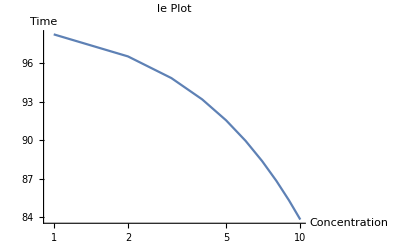
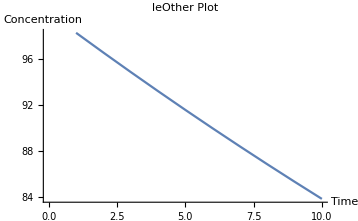

```mathematica
EulersMethod[k,h,100]
```